```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.7,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→0.7,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

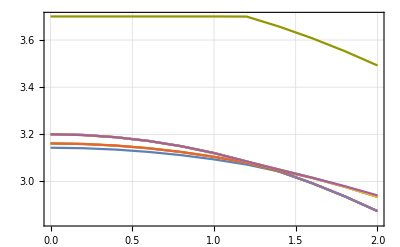

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

6.26754×10^-6

1

0.000199234

1

0.000778539

1

0.00174537

1

0.00310163

1

0.0048498

1

0.00699281

1

0.00953378

1

0.0124758

1

0.0158215

1

0.0195729

1

0.023731

1

0.028295

1

0.0332626

1

5.81448

1

5.78371

1

5.7506

1

5.71531

1

5.67808

1

5.63915

1

5.5988

2

2.

2

1.99984

2

1.99939

2

1.99862

2

1.99756

2

1.99619

2

1.99451

2

1.99253

2

1.99025

2

1.98767

2

1.98479

2

1.9816

2

1.97812

2

5.84278

2

5.81448

2

5.78371

2

5.7506

2

5.71531

2

5.67808

2

5.63915

2

5.5988

3

2.

3

1.99984

3

1.99939

3

1.99862

3

1.99756

3

1.99619

3

1.99451

3

1.99253

3

1.99025

3

1.98767

3

1.98479

3

1.9816

3

1.97812

3

5.84278

3

5.81448

3

5.78371

3

5.7506

3

5.71531

3

5.67808

3

5.63915

3

5.5988

4

2.

4

1.99984

4

1.99939

4

1.99862

4

1.99756

4

1.99619

4

1.99451

4

1.99253

4

1.99025

4

1.98767

4

1.98479

4

1.9816

4

1.97812

4

5.84278

4

5.81448

4

5.78371

4

5.7506

4

5.71531

4

5.67808

4

5.63915

4

5.5988

5

6.

5

5.99923

5

5.99692

5

5.993

5

5.98742

5

5.98007

5

5.97082

5

5.95956

5

5.94614

5

5.93043

5

5.91231

5

5.8917

5

5.86853

5

5.84278

5

5.81448

5

5.78371

5

5.7506

5

5.71531

5

5.67808

5

5.63915

5

5.5988

6

6.

6

5.99923

6

5.99692

6

5.993

6

5.98742

6

5.98007

6

5.97082

6

5.95956

6

5.94614

6

5.93043

6

5.91231

6

5.8917

6

5.86853

6

5.84278

6

0.0386287

6

0.0443859

6

0.0505234

6

1.9564

6

1.95123

6

1.94578

6

1.94008

7

6.

7

5.99923

7

5.99692

7

5.993

7

5.98742

7

5.98007

7

5.97082

7

5.95956

7

5.94614

7

5.93043

7

5.91231

7

5.8917

7

5.86853

7

1.97435

7

1.97029

7

1.96594

7

1.96131

7

1.9564

7

1.95123

7

1.94578

7

1.94008

8

6.

8

5.99923

8

5.99692

8

5.993

8

5.98742

8

5.98007

8

5.97082

8

5.95956

8

5.94614

8

5.93043

8

5.91231

8

5.8917

8

5.86853

8

1.97435

8

1.97029

8

1.96594

8

1.96131

8

1.9564

8

1.95123

8

1.94578

8

1.94008

9

6.

9

5.99923

9

5.99692

9

5.993

9

5.98742

9

5.98007

9

5.97082

9

5.95956

9

5.94614

9

5.93043

9

5.91231

9

5.8917

9

5.86853

9

1.97435

9

1.97029

9

1.96594

9

1.96131

9

0.057027

9

0.0638792

9

0.0710583

9

0.0785393

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.738079

10

0.736319

10

0.734507

10

0.732656

10

0.730781

10

0.728895

10

0.72701

10

0.725138

10

0.72329

```mathematica
data1//MatrixForm
```

(1 | 0. | 6.26754×10^-6 | 3.14284
1 | 0.1 | 0.000199234 | 3.14235
1 | 0.2 | 0.000778539 | 3.14089
1 | 0.3 | 0.00174537 | 3.13844
1 | 0.4 | 0.00310163 | 3.13501
1 | 0.5 | 0.0048498 | 3.13059
1 | 0.6 | 0.00699281 | 3.12518
1 | 0.7 | 0.00953378 | 3.11877
1 | 0.8 | 0.0124758 | 3.11135
1 | 0.9 | 0.0158215 | 3.10292
1 | 1. | 0.0195729 | 3.09346
1 | 1.1 | 0.023731 | 3.08297
1 | 1.2 | 0.028295 | 3.07144
1 | 1.3 | 0.0332626 | 3.05885
1 | 1.4 | 5.81448 | 3.04191
1 | 1.5 | 5.78371 | 3.01805
1 | 1.6 | 5.7506 | 2.99251
1 | 1.7 | 5.71531 | 2.9653
1 | 1.8 | 5.67808 | 2.93646
1 | 1.9 | 5.63915 | 2.90602
1 | 2. | 5.5988 | 2.87403
2 | 0. | 2. | 3.16107
2 | 0.1 | 1.99984 | 3.1605
2 | 0.2 | 1.99939 | 3.1588
2 | 0.3 | 1.99862 | 3.15596
2 | 0.4 | 1.99756 | 3.15199
2 | 0.5 | 1.99619 | 3.14689
2 | 0.6 | 1.99451 | 3.14065
2 | 0.7 | 1.99253 | 3.13327
2 | 0.8 | 1.99025 | 3.12476
2 | 0.9 | 1.98767 | 3.11511
2 | 1. | 1.98479 | 3.10433
2 | 1.1 | 1.9816 | 3.09241
2 | 1.2 | 1.97812 | 3.07935
2 | 1.3 | 5.84278 | 3.06407
2 | 1.4 | 5.81448 | 3.04191
2 | 1.5 | 5.78371 | 3.01805
2 | 1.6 | 5.7506 | 2.99251
2 | 1.7 | 5.71531 | 2.9653
2 | 1.8 | 5.67808 | 2.93646
2 | 1.9 | 5.63915 | 2.90602
2 | 2. | 5.5988 | 2.87403
3 | 0. | 2. | 3.16107
3 | 0.1 | 1.99984 | 3.1605
3 | 0.2 | 1.99939 | 3.1588
3 | 0.3 | 1.99862 | 3.15596
3 | 0.4 | 1.99756 | 3.15199
3 | 0.5 | 1.99619 | 3.14689
3 | 0.6 | 1.99451 | 3.14065
3 | 0.7 | 1.99253 | 3.13327
3 | 0.8 | 1.99025 | 3.12476
3 | 0.9 | 1.98767 | 3.11511
3 | 1. | 1.98479 | 3.10433
3 | 1.1 | 1.9816 | 3.09241
3 | 1.2 | 1.97812 | 3.07935
3 | 1.3 | 5.84278 | 3.06407
3 | 1.4 | 5.81448 | 3.04191
3 | 1.5 | 5.78371 | 3.01805
3 | 1.6 | 5.7506 | 2.99251
3 | 1.7 | 5.71531 | 2.9653
3 | 1.8 | 5.67808 | 2.93646
3 | 1.9 | 5.63915 | 2.90602
3 | 2. | 5.5988 | 2.87403
4 | 0. | 2. | 3.16107
4 | 0.1 | 1.99984 | 3.1605
4 | 0.2 | 1.99939 | 3.1588
4 | 0.3 | 1.99862 | 3.15596
4 | 0.4 | 1.99756 | 3.15199
4 | 0.5 | 1.99619 | 3.14689
4 | 0.6 | 1.99451 | 3.14065
4 | 0.7 | 1.99253 | 3.13327
4 | 0.8 | 1.99025 | 3.12476
4 | 0.9 | 1.98767 | 3.11511
4 | 1. | 1.98479 | 3.10433
4 | 1.1 | 1.9816 | 3.09241
4 | 1.2 | 1.97812 | 3.07935
4 | 1.3 | 5.84278 | 3.06407
4 | 1.4 | 5.81448 | 3.04191
4 | 1.5 | 5.78371 | 3.01805
4 | 1.6 | 5.7506 | 2.99251
4 | 1.7 | 5.71531 | 2.9653
4 | 1.8 | 5.67808 | 2.93646
4 | 1.9 | 5.63915 | 2.90602
4 | 2. | 5.5988 | 2.87403
5 | 0. | 6. | 3.2
5 | 0.1 | 5.99923 | 3.19922
5 | 0.2 | 5.99692 | 3.19687
5 | 0.3 | 5.993 | 3.19294
5 | 0.4 | 5.98742 | 3.18744
5 | 0.5 | 5.98007 | 3.18033
5 | 0.6 | 5.97082 | 3.17162
5 | 0.7 | 5.95956 | 3.16127
5 | 0.8 | 5.94614 | 3.14928
5 | 0.9 | 5.93043 | 3.13562
5 | 1. | 5.91231 | 3.12029
5 | 1.1 | 5.8917 | 3.10325
5 | 1.2 | 5.86853 | 3.08452
5 | 1.3 | 5.84278 | 3.06407
5 | 1.4 | 5.81448 | 3.04191
5 | 1.5 | 5.78371 | 3.01805
5 | 1.6 | 5.7506 | 2.99251
5 | 1.7 | 5.71531 | 2.9653
5 | 1.8 | 5.67808 | 2.93646
5 | 1.9 | 5.63915 | 2.90602
5 | 2. | 5.5988 | 2.87403
6 | 0. | 6. | 3.2
6 | 0.1 | 5.99923 | 3.19922
6 | 0.2 | 5.99692 | 3.19687
6 | 0.3 | 5.993 | 3.19294
6 | 0.4 | 5.98742 | 3.18744
6 | 0.5 | 5.98007 | 3.18033
6 | 0.6 | 5.97082 | 3.17162
6 | 0.7 | 5.95956 | 3.16127
6 | 0.8 | 5.94614 | 3.14928
6 | 0.9 | 5.93043 | 3.13562
6 | 1. | 5.91231 | 3.12029
6 | 1.1 | 5.8917 | 3.10325
6 | 1.2 | 5.86853 | 3.08452
6 | 1.3 | 5.84278 | 3.06407
6 | 1.4 | 0.0386287 | 3.0452
6 | 1.5 | 0.0443859 | 3.03049
6 | 1.6 | 0.0505234 | 3.0147
6 | 1.7 | 1.9564 | 2.99718
6 | 1.8 | 1.95123 | 2.9774
6 | 1.9 | 1.94578 | 2.95652
6 | 2. | 1.94008 | 2.93454
7 | 0. | 6. | 3.2
7 | 0.1 | 5.99923 | 3.19922
7 | 0.2 | 5.99692 | 3.19687
7 | 0.3 | 5.993 | 3.19294
7 | 0.4 | 5.98742 | 3.18744
7 | 0.5 | 5.98007 | 3.18033
7 | 0.6 | 5.97082 | 3.17162
7 | 0.7 | 5.95956 | 3.16127
7 | 0.8 | 5.94614 | 3.14928
7 | 0.9 | 5.93043 | 3.13562
7 | 1. | 5.91231 | 3.12029
7 | 1.1 | 5.8917 | 3.10325
7 | 1.2 | 5.86853 | 3.08452
7 | 1.3 | 1.97435 | 3.06517
7 | 1.4 | 1.97029 | 3.04985
7 | 1.5 | 1.96594 | 3.03342
7 | 1.6 | 1.96131 | 3.01586
7 | 1.7 | 1.9564 | 2.99718
7 | 1.8 | 1.95123 | 2.9774
7 | 1.9 | 1.94578 | 2.95652
7 | 2. | 1.94008 | 2.93454
8 | 0. | 6. | 3.2
8 | 0.1 | 5.99923 | 3.19922
8 | 0.2 | 5.99692 | 3.19687
8 | 0.3 | 5.993 | 3.19294
8 | 0.4 | 5.98742 | 3.18744
8 | 0.5 | 5.98007 | 3.18033
8 | 0.6 | 5.97082 | 3.17162
8 | 0.7 | 5.95956 | 3.16127
8 | 0.8 | 5.94614 | 3.14928
8 | 0.9 | 5.93043 | 3.13562
8 | 1. | 5.91231 | 3.12029
8 | 1.1 | 5.8917 | 3.10325
8 | 1.2 | 5.86853 | 3.08452
8 | 1.3 | 1.97435 | 3.06517
8 | 1.4 | 1.97029 | 3.04985
8 | 1.5 | 1.96594 | 3.03342
8 | 1.6 | 1.96131 | 3.01586
8 | 1.7 | 1.9564 | 2.99718
8 | 1.8 | 1.95123 | 2.9774
8 | 1.9 | 1.94578 | 2.95652
8 | 2. | 1.94008 | 2.93454
9 | 0. | 6. | 3.2
9 | 0.1 | 5.99923 | 3.19922
9 | 0.2 | 5.99692 | 3.19687
9 | 0.3 | 5.993 | 3.19294
9 | 0.4 | 5.98742 | 3.18744
9 | 0.5 | 5.98007 | 3.18033
9 | 0.6 | 5.97082 | 3.17162
9 | 0.7 | 5.95956 | 3.16127
9 | 0.8 | 5.94614 | 3.14928
9 | 0.9 | 5.93043 | 3.13562
9 | 1. | 5.91231 | 3.12029
9 | 1.1 | 5.8917 | 3.10325
9 | 1.2 | 5.86853 | 3.08452
9 | 1.3 | 1.97435 | 3.06517
9 | 1.4 | 1.97029 | 3.04985
9 | 1.5 | 1.96594 | 3.03342
9 | 1.6 | 1.96131 | 3.01586
9 | 1.7 | 0.057027 | 2.99782
9 | 1.8 | 0.0638792 | 2.97985
9 | 1.9 | 0.0710583 | 2.96078
9 | 2. | 0.0785393 | 2.94062
10 | 0. | 3.75 | 3.7
10 | 0.1 | 3.75 | 3.7
10 | 0.2 | 3.75 | 3.7
10 | 0.3 | 3.75 | 3.7
10 | 0.4 | 3.75 | 3.7
10 | 0.5 | 3.75 | 3.7
10 | 0.6 | 3.75 | 3.7
10 | 0.7 | 3.75 | 3.7
10 | 0.8 | 3.75 | 3.7
10 | 0.9 | 3.75 | 3.7
10 | 1. | 3.75 | 3.7
10 | 1.1 | 3.75 | 3.7
10 | 1.2 | 0.738079 | 3.69947
10 | 1.3 | 0.736319 | 3.67885
10 | 1.4 | 0.734507 | 3.65667
10 | 1.5 | 0.732656 | 3.63295
10 | 1.6 | 0.730781 | 3.60772
10 | 1.7 | 0.728895 | 3.58099
10 | 1.8 | 0.72701 | 3.55279
10 | 1.9 | 0.725138 | 3.52313
10 | 2. | 0.72329 | 3.49204)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;14,1;;4]];
tmp02 = data1[[120;;122,1;;4]];
tmp03 = data1[[186;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;34,1;;4]];
tmp02 = data1[[140;;147, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.14284 | 6.26754×10^-6
0.1 | 3.14235 | 0.000199234
0.2 | 3.14089 | 0.000778539
0.3 | 3.13844 | 0.00174537
0.4 | 3.13501 | 0.00310163
0.5 | 3.13059 | 0.0048498
0.6 | 3.12518 | 0.00699281
0.7 | 3.11877 | 0.00953378
0.8 | 3.11135 | 0.0124758
0.9 | 3.10292 | 0.0158215
1. | 3.09346 | 0.0195729
1.1 | 3.08297 | 0.023731
1.2 | 3.07144 | 0.028295
1.3 | 3.05885 | 0.0332626
1.4 | 3.0452 | 0.0386287
1.5 | 3.03049 | 0.0443859
1.6 | 3.0147 | 0.0505234
1.7 | 2.99782 | 0.057027
1.8 | 2.97985 | 0.0638792
1.9 | 2.96078 | 0.0710583
2. | 2.94062 | 0.0785393)

(0. | 3.16107 | 2.
0.1 | 3.1605 | 1.99984
0.2 | 3.1588 | 1.99939
0.3 | 3.15596 | 1.99862
0.4 | 3.15199 | 1.99756
0.5 | 3.14689 | 1.99619
0.6 | 3.14065 | 1.99451
0.7 | 3.13327 | 1.99253
0.8 | 3.12476 | 1.99025
0.9 | 3.11511 | 1.98767
1. | 3.10433 | 1.98479
1.1 | 3.09241 | 1.9816
1.2 | 3.07935 | 1.97812
1.3 | 3.06517 | 1.97435
1.4 | 3.04985 | 1.97029
1.5 | 3.03342 | 1.96594
1.6 | 3.01586 | 1.96131
1.7 | 2.99718 | 1.9564
1.8 | 2.9774 | 1.95123
1.9 | 2.95652 | 1.94578
2. | 2.93454 | 1.94008)

(0. | 3.2 | 6.
0.1 | 3.19922 | 5.99923
0.2 | 3.19687 | 5.99692
0.3 | 3.19294 | 5.993
0.4 | 3.18744 | 5.98742
0.5 | 3.18033 | 5.98007
0.6 | 3.17162 | 5.97082
0.7 | 3.16127 | 5.95956
0.8 | 3.14928 | 5.94614
0.9 | 3.13562 | 5.93043
1. | 3.12029 | 5.91231
1.1 | 3.10325 | 5.8917
1.2 | 3.08452 | 5.86853
1.3 | 3.06407 | 5.84278
1.4 | 3.04191 | 5.81448
1.5 | 3.01805 | 5.78371
1.6 | 2.99251 | 5.7506
1.7 | 2.9653 | 5.71531
1.8 | 2.93646 | 5.67808
1.9 | 2.90602 | 5.63915
2. | 2.87403 | 5.5988)

```mathematica
|
```

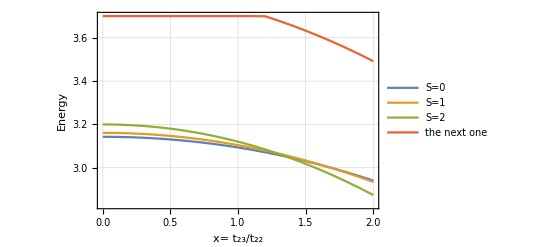

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

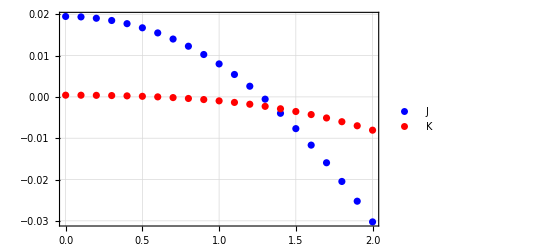

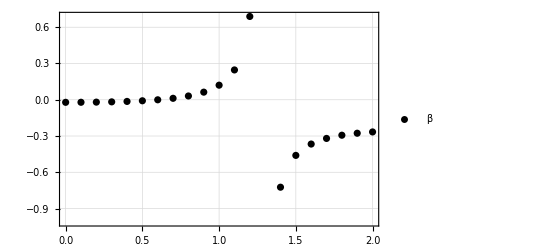

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```